```mathematica
Timing[
$HistoryLength=3;
ClearAll[Lz,XY,XZ,YZ];

Lz=20;(*Lengrh of simulation*)
R=0.08;(*Solenoid radius*)

(*List of initial particle radius and energy*)

Rad[1]={"4e-3","8e-3","1.6e-2","2.4e-2","3.2e-2","4e-2","4.8e-2","5.6e-2","6.4e-2","7.2e-2"};
Eneg[1]={"4.823e5","1.928e6","1.198e7","4.705e7","1.763e8","3.633e8","5.870e8","8.333e8","1.094e9","1.365e9","1.641e9","1.923e9","2.208e9"};

(* Read in data file: put your directory path here *)

Table[orb[i,j]=Import["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/solenoid_scipy/result/pthe_0_sl30cm/alldata_amp"<>ToString[Rad[1][[j]]]<>"_velo0_kene"<>ToString[Eneg[1][[i]]]<>"_sleng30cm_step6001.dat","Table"],{i,1,13},{j,1,10}];

LENG[1]=Length[orb[1,1]];
Table[X[i,j]=orb[i,j][[All,1]],{i,1,13},{j,1,10}];
Table[Vx[i,j]=orb[i,j][[All,2]],{i,1,13},{j,1,10}];
Table[Y[i,j]=orb[i,j][[All,3]],{i,1,13},{j,1,10}];
Table[Vy[i,j]=orb[i,j][[All,4]],{i,1,13},{j,1,10}];
Table[Z[i,j]=orb[i,j][[All,5]],{i,1,13},{j,1,10}];
Table[Vz[i,j]=orb[i,j][[All,6]],{i,1,13},{j,1,10}];
Table[Xy[i,j]=orb[i,j][[All,{1,3}]],{i,1,13},{j,1,10}];
Table[RZ[i,j]=Table[{Z[i,j][[n]],(X[i,j][[n]]^2+Y[i,j][[n]]^2)^0.5},{n,1,LENG[1]}],{i,1,13},{j,1,10}];
Table[PT[i,j]=orb[i,j][[All,{5,7}]],{i,1,13},{j,1,10}];
Table[RK[i,j]=orb[i,j][[All,8]],{i,1,13},{j,1,10}];

Rad[2]={0.004,0.008,0.016,0.024,0.032,0.04,0.048,0.056,0.064,0.072};

Table[ToRK[i,j]={Rad[2][[j]]/R,Abs[Sum[RK[i,j][[n]]*Vz[i,j][[n]]*(Lz/((Vz[i,j][[1]])*(LENG[1]-1))),{n,1,LENG[1]}]]},{i,1,13},{j,1,10}];

]
```

{210.67418,Null}

```mathematica
(*Calculation of theoretical radial kick*)

ClearAll[Brho,Rad];
l=0.3;(*Solenoid length*)
Rad[2]={0.004,0.008,0.016,0.024,0.032,0.04,0.048,0.056,0.064,0.072};
Brho[1]={0.1,0.2,0.5,1,2,3,4,5,6,7,8,9,10};
Bz00[z_]=(z+l/2)/(√((z+l/2)^2+R^2))-(z-l/2)/(√((z-l/2)^2+R^2));(*Bz field*)
Bz1[z_]:=((z+l/2)/(√((z+l/2)^2+R^2))-(z-l/2)/(√((z-l/2)^2+R^2)))/Bz00[0];(*Scaled Bz field*)
Bz2[z_]:=Bz1'[z];(*Scaled Bz field*)
Bz3[z_]:=Bz2'[z];(*Scaled Bz field*)
Bz4[z_]:=Bz3'[z];(*Scaled Bz field*)
Bz5[z_]:=Bz4'[z];(*Scaled Bz field*)
Bz6[z_]:=Bz5'[z];(*Scaled Bz field*)

Timing[
Table[RD1[i,j]=-1/4*NIntegrate[(Bz1[z]/(Brho[1][[i]]))^2*Rad[2][[j]],{z,-∞,∞}],{i,1,13},{j,1,10}];
Table[RD2[i,j]=-1/8*NIntegrate[(Bz2[z]/(Brho[1][[i]]))^2*Rad[2][[j]]^3,{z,-∞,∞}],{i,1,13},{j,1,10}];
Table[RD3[i,j]=-5/256*NIntegrate[(Bz3[z]/(Brho[1][[i]]))^2*Rad[2][[j]]^5,{z,-∞,∞}],{i,1,13},{j,1,10}];
Table[RD4[i,j]=-7/4608*NIntegrate[(Bz4[z]/(Brho[1][[i]]))^2*Rad[2][[j]]^7,{z,-∞,∞}],{i,1,13},{j,1,10}];
Table[RD5[i,j]=-7/98304*NIntegrate[(Bz5[z]/(Brho[1][[i]]))^2*Rad[2][[j]]^9,{z,-∞,∞}],{i,1,13},{j,1,10}];

Table[TheoToRKLin[i,j]={Rad[2][[j]]/R,-RD1[i,j]},{i,1,13},{j,1,10}];

Table[TheoToRK[i,j]={Rad[2][[j]]/R,-(RD1[i,j]+RD2[i,j]+RD3[i,j]+RD4[i,j]+RD5[i,j])},{i,1,13},{j,1,10}];

]
```

{8.97948,Null}

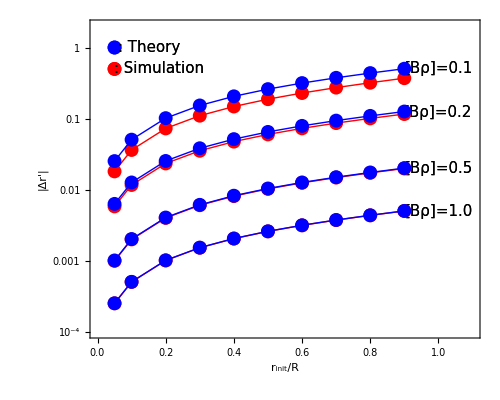

```mathematica
(*LogPlot of comparison between theory and simulations*)

GList[1]={{{1.0,5*10^-1}},{{1.0,1.2*10^-1}},{{1.0,2*10^-2}},{{1.0,5*10^-3}}};

GList[2]={{{0.15,1}},{{0.18,0.5}}};

Comp[1]=Show[

ListLogPlot[Table[ToRK[1,i],{i,1,10}],PlotRange->{{0,1.1},{0.0001,2}},FrameLabel->{"r_init/R","|Δr'|"},LabelStyle->Directive[18],Frame->True,AspectRatio->0.8,Axes->None,Joined->True,PlotStyle->{Red},ImageSize->{500,400}],
ListLogPlot[Table[ToRK[1,i],{i,1,10}],PlotRange->{{0,1},{0.000001,0.1}},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Red,PointSize[0.02]}],
ListLogPlot[Table[TheoToRK[1,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,PlotStyle->{Blue}],
ListLogPlot[Table[TheoToRK[1,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Blue,PointSize[0.02]}],

ListLogPlot[Table[ToRK[2,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,PlotStyle->{Red}],
ListLogPlot[Table[ToRK[2,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Red,PointSize[0.02]}],
ListLogPlot[Table[TheoToRK[2,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,PlotStyle->{Blue}],
ListLogPlot[Table[TheoToRK[2,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Blue,PointSize[0.02]}],

ListLogPlot[Table[ToRK[3,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,PlotStyle->{Red}],
ListLogPlot[Table[ToRK[3,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Red,PointSize[0.02]}],
ListLogPlot[Table[TheoToRK[3,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,PlotStyle->{Blue}],
ListLogPlot[Table[TheoToRK[3,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Blue,PointSize[0.02]}],

ListLogPlot[Table[ToRK[4,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,PlotStyle->{Red}],
ListLogPlot[Table[ToRK[4,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Red,PointSize[0.02]}],
ListLogPlot[Table[TheoToRK[4,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,PlotStyle->{Blue}],
ListLogPlot[Table[TheoToRK[4,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Blue,PointSize[0.02]}],

ListLogPlot[GList[1],PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Black},PlotMarkers->{{"[Bρ]=0.1",15},{"[Bρ]=0.2",15},{"[Bρ]=0.5",15},{"[Bρ]=1.0",15}},BaseStyle->{FontFamily->"Times",FontSize->15}],

ListLogPlot[GList[2],PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Black},PlotMarkers->{{": Theory",15},{": Simulation",15}},BaseStyle->{FontFamily->"Times",FontSize->15}],

ListLogPlot[{{0.05,1}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Blue,PointSize[0.02]}],
ListLogPlot[{{0.05,0.5}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Red,PointSize[0.02]}]
]
```

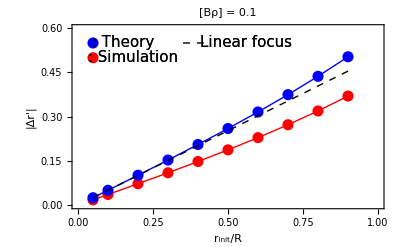

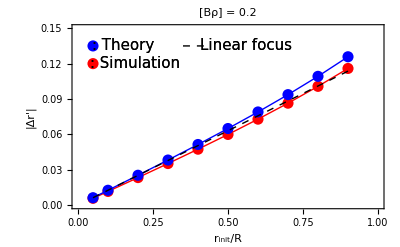

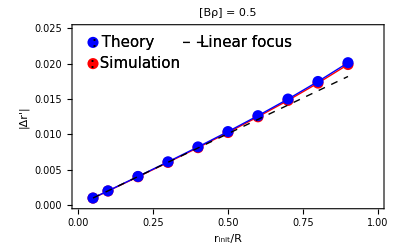

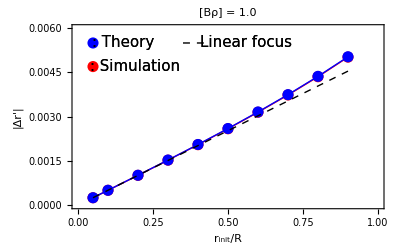

```mathematica
(*LinearPlot of comparison between theory and simulations*)

GList[1]={{{1.0,5*10^-1}},{{1.0,1.2*10^-1}},{{1.0,2*10^-2}},{{1.0,5*10^-3}}};

GList[2]={{{0.15,0.55}},{{0.185,0.5}},{{0.56,0.55}}};

Comp[2]=Show[

ListPlot[Table[ToRK[1,i],{i,1,10}],PlotRange->{{0,1},{0,0.6}},FrameLabel->{"r_init/R","|Δr'|"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,PlotStyle->{Red},PlotLabel->Style["[Bρ] = 0.1",17]],
ListPlot[Table[ToRK[1,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Red,PointSize[0.02]}],
ListPlot[Table[TheoToRK[1,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,PlotStyle->{Blue}],
ListPlot[Table[TheoToRK[1,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Blue,PointSize[0.02]}],
ListPlot[Table[TheoToRKLin[1,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,PlotStyle->{Black,Dashed}],
ListPlot[{{0.35,0.55},{0.43,0.55}},PlotRange->All,LabelStyle->Directive[15],Joined->True,PlotStyle->{Black,Dashed}],

ListPlot[GList[2],PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Black},PlotMarkers->{{": Theory",15},{": Simulation",15},{"Linear focus",15}},BaseStyle->{FontFamily->"Times",FontSize->15}],

ListPlot[{{0.05,0.55}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Blue,PointSize[0.02]}],
ListPlot[{{0.05,0.5}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Red,PointSize[0.02]}]
]

GList[3]={{{0.15,0.135}},{{0.19,0.12}},{{0.56,0.135}}};

Comp[3]=Show[

ListPlot[Table[ToRK[2,i],{i,1,10}],PlotRange->{{0,1},{0,0.15}},FrameLabel->{"r_init/R","|Δr'|"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,PlotStyle->{Red},PlotLabel->Style["[Bρ] = 0.2",17]],
ListPlot[Table[ToRK[2,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Red,PointSize[0.02]}],
ListPlot[Table[TheoToRK[2,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,PlotStyle->{Blue}],
ListPlot[Table[TheoToRK[2,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Blue,PointSize[0.02]}],
ListPlot[Table[TheoToRKLin[2,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,PlotStyle->{Black,Dashed}],
ListPlot[{{0.35,0.135},{0.43,0.135}},PlotRange->All,LabelStyle->Directive[15],Joined->True,PlotStyle->{Black,Dashed}],

ListPlot[GList[3],PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Black},PlotMarkers->{{": Theory",15},{": Simulation",15},{"Linear focus",15}},BaseStyle->{FontFamily->"Times",FontSize->15}],

ListPlot[{{0.05,0.135}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Blue,PointSize[0.02]}],
ListPlot[{{0.05,0.12}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Red,PointSize[0.02]}]
]

GList[4]={{{0.15,0.023}},{{0.19,0.02}},{{0.56,0.023}}};

Comp[4]=Show[

ListPlot[Table[ToRK[3,i],{i,1,10}],PlotRange->{{0,1},{0,0.025}},FrameLabel->{"r_init/R","|Δr'|"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,PlotStyle->{Red},PlotLabel->Style["[Bρ] = 0.5",17]],
ListPlot[Table[ToRK[3,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Red,PointSize[0.02]}],
ListPlot[Table[TheoToRK[3,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,PlotStyle->{Blue}],
ListPlot[Table[TheoToRK[3,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Blue,PointSize[0.02]}],
ListPlot[Table[TheoToRKLin[3,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,PlotStyle->{Black,Dashed}],
ListPlot[{{0.35,0.023},{0.43,0.023}},PlotRange->All,LabelStyle->Directive[15],Joined->True,PlotStyle->{Black,Dashed}],

ListPlot[GList[4],PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Black},PlotMarkers->{{": Theory",15},{": Simulation",15},{"Linear focus",15}},BaseStyle->{FontFamily->"Times",FontSize->15}],

ListPlot[{{0.05,0.023}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Blue,PointSize[0.02]}],
ListPlot[{{0.05,0.02}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Red,PointSize[0.02]}]
]

GList[5]={{{0.15,0.0055}},{{0.19,0.0047}},{{0.56,0.0055}}};

Comp[5]=Show[

ListPlot[Table[ToRK[4,i],{i,1,10}],PlotRange->{{0,1},{0,0.006}},FrameLabel->{"r_init/R","|Δr'|"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,PlotStyle->{Red},PlotLabel->Style["[Bρ] = 1.0",17]],
ListPlot[Table[ToRK[4,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Red,PointSize[0.02]}],
ListPlot[Table[TheoToRK[4,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,PlotStyle->{Blue}],
ListPlot[Table[TheoToRK[4,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Blue,PointSize[0.02]}],
ListPlot[Table[TheoToRKLin[4,i],{i,1,10}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,PlotStyle->{Black,Dashed}],
ListPlot[{{0.35,0.0055},{0.43,0.0055}},PlotRange->All,LabelStyle->Directive[15],Joined->True,PlotStyle->{Black,Dashed}],

ListPlot[GList[5],PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Black},PlotMarkers->{{": Theory",15},{": Simulation",15},{"Linear focus",15}},BaseStyle->{FontFamily->"Times",FontSize->15}],

ListPlot[{{0.05,0.0055}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Blue,PointSize[0.02]}],
ListPlot[{{0.05,0.0047}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Red,PointSize[0.02]}]
]
```

```mathematica
(*Export graphic data to the directory on your computer:you have to specify the directory where you want to export*)

Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/Ptheta0/Pthe0_sol30cm_Comp_Sum_init_low_Brho.eps",Comp[1],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/Ptheta0/Pthe0_sol30cm_Comp_Brho0.1_init_low_Brho.eps",Comp[2],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/Ptheta0/Pthe0_sol30cm_Comp_Brho0.2_init_low_Brho.eps",Comp[3],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/Ptheta0/Pthe0_sol30cm_Comp_Brho0.5_init_low_Brho.eps",Comp[4],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/Ptheta0/Pthe0_sol30cm_Comp_Brho1.0_init_low_Brho.eps",Comp[5],"EPS"];
```

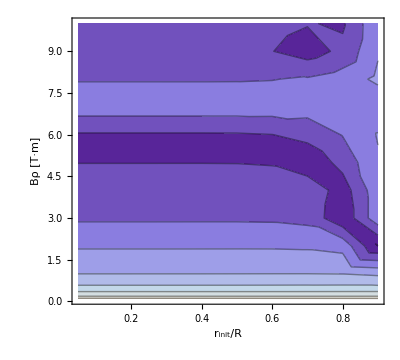

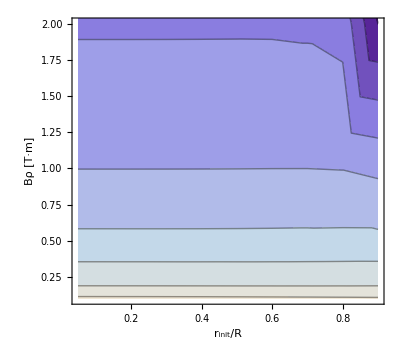

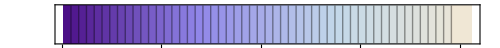

```mathematica
(*Contour Plot of difference between theory and simulations*)

RdError3d[1]=Table[{Rad[2][[j]]/R,Brho[1][[i]],Log[10,Abs[100*(ToRK[i,j][[2]]-TheoToRK[i,j][[2]])/ToRK[i,j][[2]]]]},{j,1,10},{i,1,13}];
ErrPlot[1]=ListContourPlot[Flatten[RdError3d[1],1],PlotRange->{{0.05,0.9},{0.1,10},All},AspectRatio->0.9,FrameLabel->{"r_init/R","Bρ [T·m]"},LabelStyle->Directive[18],ClippingStyle->{Black}]
ErrPlot[2]=ListContourPlot[Flatten[RdError3d[1],1],PlotRange->{{0.05,0.9},{0.1,2},All},AspectRatio->0.9,FrameLabel->{"r_init/R","Bρ [T·m]"},LabelStyle->Directive[18],ClippingStyle->{Black}]

(*Making Label of Contur Plot*)

MAXDIF=Max[Table[Log[10,Abs[100*(ToRK[i,j][[2]]-TheoToRK[i,j][[2]])/ToRK[i,j][[2]]]],{j,1,10},{i,1,13}]];
MINDIF=Min[Table[Log[10,Abs[100*(ToRK[i,j][[2]]-TheoToRK[i,j][[2]])/ToRK[i,j][[2]]]],{j,1,10},{i,1,13}]];
label1=ListContourPlot[{{MINDIF,0,0},{MINDIF,1,0},{MAXDIF,0,1},{MAXDIF,1,1}},Contours->50,PlotRange->{{MINDIF,MAXDIF},{0,1},All},AspectRatio->0.05,PlotLabel->Style["Radial kick difference between theory and simulations [%]",20]
,FrameTicksStyle->20,ImageSize->500,FrameTicks->{{None,None},{{{1.4772,"30"},{0.4772,"3"},{-0.5228,"0.3"},{-1.5228,"0.03"},{-2.5228,"0.003"}},None}}]
```

```mathematica
(*Export graphic data to the directory on your computer:you have to specify the directory where you want to export*)

Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/Ptheta0/Pthe0_Comp_3D_init_log.eps",ErrPlot[1],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/Ptheta0/Pthe0_Comp_3D_init_low_brho_log.eps",ErrPlot[2],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/Ptheta0/Diff_Label.eps",label1,"EPS"];
```